628.319

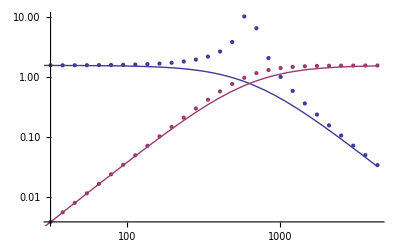

```mathematica
sk=Import["~/Dropbox/vafmpro/pyvafm/examples/test_filters.log","Table"];
sk[[All,1]]*=2Pi;
w0=2Pi 100.
gain=Pi/2;
Q=10000Sqrt[2]/2;
Show[
ListLogLogPlot[{sk[[All,{1,2}]],sk[[All,{1,3}]]}]
,LogLogPlot[{
gain(w0^2)/(s^2+(w0 s/Q)+w0^2),
gain(s^2)/(s^2+w0 s/Q+w0^2)
},{s,1,sk[[-1,1]]},PlotRange->All]
]
```

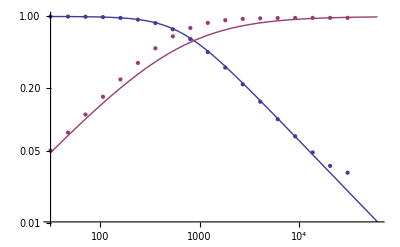

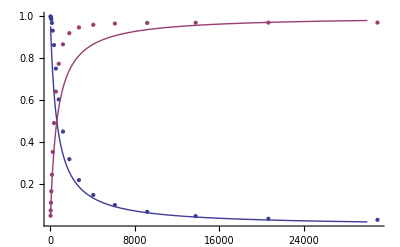

```mathematica
sk=Import["~/Dropbox/vafmpro/pyvafm/examples/test_filters2.log","Table"];
sk[[All,1]]*=2Pi;
w0=2Pi 100;
o=1;

Show[
LogLogPlot[{Sqrt[(1/((s/w0)^2+1))^o],(s/(s+w0))^o
},{s,2Pi 5,sk[[-1,1]]2},PlotRange->All],
ListLogLogPlot[{sk[[All,{1,2}]],sk[[All,{1,3}]]}]
]
Show[
ListPlot[{sk[[All,{1,2}]],sk[[All,{1,3}]]}],
Plot[{(1/(s/w0+1))^o,(s/(s+w0))^o
},{s,2Pi 5,30000},PlotRange->All]
]
```

```mathematica
Manipulate[LogLogPlot[{r/(r+1/(s c)),1/(r c s + 1)},{s,1,10000}],{r,0,10},{c,0,10}]
```

```mathematica
0.125663706144(0.431456045681-0.752058409846)+0.0381459784405
```

-0.0021421

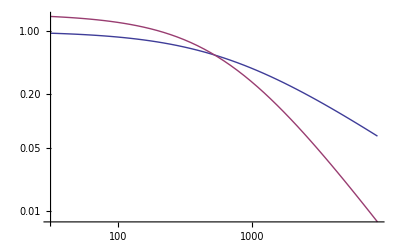

```mathematica
LogLogPlot[{(1/(s/w0+1))^1,gain(w0^2)/(s^2+w0 s/Q+w0^2)
},{s,2Pi 5,sk[[-1,1]]2},PlotRange->All]
```